```mathematica
f[x_,y_]:=x^2+3(y-1)^2+x y+3 Sign[x]
```

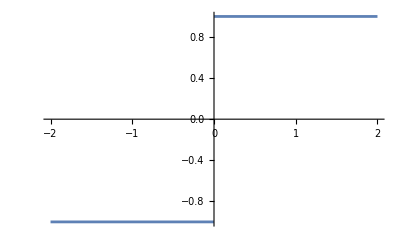

```mathematica
Plot[Sign[x],{x,-2,2}]
```

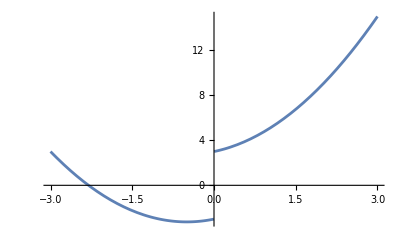

```mathematica
Plot[f[x,1],{x,-3,3},PlotRange->All]
```

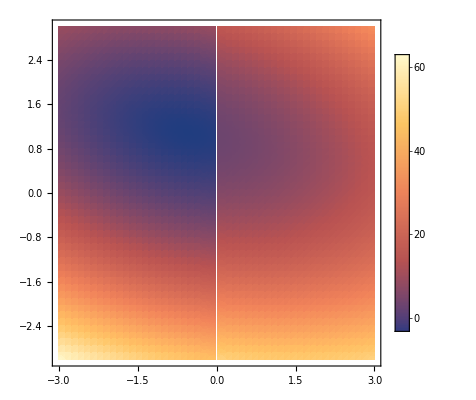

```mathematica
DensityPlot[f[x,y],{x,-3,3},{y,-3,3},PlotRange->All,PlotPoints->50,PlotLegends->Automatic]
```

```mathematica
NMinimize[{f[x,y],-5<x<5,-5<y<5},{x,y}]
```

{-3.27273,{x→-0.545455,y→1.09091}}

```mathematica
(*NMinimze can deal with all kinds of constraints etc. It internally chooses teh rigth algorithm.*)
```

f should now be your cost function, e . g . r1 and r2 are the tunneling ratios, and we want r10  and r20 , and the flux is xi and xi0, then you can try  f=a (r1-r10)^2+b (r2-r20)^2+c (φ-φ0 )^2 and play with a,b,c to optimise...

#### import brute force neighbourhood results

```mathematica
filename = "Heff_omega=8,alpha=1,beta=2.csv";
neighbourhoodData= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
```

$Aborted

```mathematica
(* Define J23 tunnelling val*)
J23[A2_, A3_, omega_, phi3_]:= (omega/2/π)*NIntegrate[Cos[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t,-π/omega,π/omega}]+(omega*ⅈ/2/π)*NIntegrate[Sin[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t, -π/omega,π/omega}]
(* define flux xi*)
Xi[A2_, A3_, omega_, phi3_]:=Arg[BesselJ[0,A3/2/omega]*BesselJ[0,A2/omega]*J23[A2, A3, omega, phi3]]
(*Define function to retrieve middle value of 3x1 list *)
Mid[v1_, v2_, v3_]:=v1+v2+v3-Max[v1, v2, v3] - Min[v1, v2, v3]
(*define tunnelling ratios*)
R1[A2_, A3_, omega_, phi3_]:= Mid[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]
R2[A2_, A3_ ,omega_, phi3_]:=Min[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]

r10= 0.9; (*x val on rel triangle *)
r20 = 0.7; (* y val on rel triangle *)

(*func to minimise*)
f[A2_, A3_, omega_, phi3_, r10_, r20_, xi0_, a_, b_, c_]:= a*(Xi[A2, A3, omega, phi3]- xi0)^2 + b*(R1[A2, A3, omega, phi3] - r10)^2+ c*(R2[A2, A3, omega, phi3] - r20)^2
```

```mathematica
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_precision2.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data"];
a = 100; b = 100; c = 100;

(* first val *)
sol = FindMinimum[{f[A2, A3, omega, phi3, r10, r20, 0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, -2*π≤phi3<2*π},
 {{A2,20},{A3,20}, {omega,8}, {phi3,0}},
PrecisionGoal->5,
AccuracyGoal->5,
MaxIterations->Infinity
];

A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
omegac = sol[[2,3,2]];
phic = sol[[2,4,2]];

dataTable = Append[dataTable, {"FindMinimum,PG=5,AG=5,MI=inf", r10,r20, 0, a, b, c, A2c, A3c, omegac, phic,  sol[[1]]}];

Nvals = 25;
For[ii = 1, ii≤ Nvals, ii++,
Print[ii];
(*Do minimisation*)
xi0= ii*π/Nvals; 
(*sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},{A2, A3, omega, phi3}];
sol = NMinimize[{f[A2, A3,  omegaI, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 0≤phi3<2*π},{A2, A3,  phi3}];*)
sol = FindMinimum[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, -2*Pi≤phi3<2*π},
 {{A2,A2c},{A3,A3c}, {omega,omegac}, {phi3,phic}},
PrecisionGoal->5,
AccuracyGoal->5,
MaxIterations->Infinity
];
errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
omegac = sol[[2,3,2]];
phic = sol[[2,4,2]];
(*check answers*)
(*xi = Xi[A2c, A3c, omegac, phic] /π;
r1 = R1[A2c, A3c, omegac, phic] ;
r2 = R2[A2c, A3c, omegac, phic] ;*)
dataTable = Append[dataTable, {"FindMinimum,PG=5,AG=5,MI=inf", r10,r20, xi0/Pi, a, b, c, A2c, A3c, omegac, phic, errorc}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-0.335954}. NIntegrate obtained 4.77049×10^-17 and 4.00287×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-0.139604}. NIntegrate obtained -2.66714×10^-17 and 4.1495×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.331328}. NIntegrate obtained -2.73219×10^-17 and 4.15795×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.37103747100749891775224153372958468821707356255501508712768554688}. NIntegrate obtained 8.06629×10^-13 and 6.18707×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-0.291366}. NIntegrate obtained 8.06662×10^-13 and 5.02003×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.37103747100749891775224153372958468821707356255501508712768554688}. NIntegrate obtained 8.0661×10^-13 and 6.18712×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

20

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

21

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

22

23

$Aborted

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

#### try import initial conditions

```mathematica
filename = "initial_conditions.csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,5]];
initialA3s = initialConds[[All,6]];
initialVarphis = initialConds[[All,8]];
initialXi0Fracs = initialConds[[All,3]];
```

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

```mathematica
r10= 0.9; (*x val on rel triangle *)
r20 = 0.9; (* y val on rel triangle *)

(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data"];
a = 1; b = 10; c = 10;

Nvals = 50;
For[ii = 0, ii≤ Nvals-1, ii++,
Print[ii,", ", initialXi0Fracs [[ii+1]],", ",  initialA2s[[ii+1]], ", ",  initialA3s[[ii+1]],", ",  initialVarphis[[ii+1]]];
(*Do minimisation*)
xi0= initialXi0Fracs[[ii+1]]*π; 
(*sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},{A2, A3, omega, phi3}];
sol = NMinimize[{f[A2, A3,  omegaI, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 0≤phi3<2*π},{A2, A3,  phi3}];*)
sol = FindMinimum[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 7.9<= omega, -2*Pi≤phi3<2*π},
 {{A2,initialA2s[[ii+1]]},{A3,initialA3s[[ii+1]]}, {omega,8}, {phi3,initialVarphis[[ii+1]]*Pi}},
PrecisionGoal->4,
AccuracyGoal->4,
MaxIterations->Infinity
];

errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
omegac = sol[[2,3,2]];
phic = sol[[2,4,2]];
Print["                           ", A2c,", ",  A3c ", ",  omegac,", ", phic, ", ", errorc];
dataTable = Append[dataTable, {"FindMinimum,PG=4,AG=4,MI=inf,imported_ic_smart4.0", r10,r20, xi0/Pi, a, b, c, A2c, A3c, omegac, phic, errorc, initialA2s[[ii+1]], initialA3s[[ii+1]], 8, initialVarphis[[ii+1]]}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

0, 0., 33.5, 54.5, 0.02

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

36.3707, 61.6718 , 8.75981, -5.64592×10^-6, 1.17534×10^-10

1, 0.02, 34., 54.5, 0.06

36.632, 61.2139 , 8.76217, 0.117214, 1.61577×10^-10

2, 0.04, 34., 52.5, 0.08

38.7686, 62.4514 , 9.11561, 0.217069, 1.89683×10^-10

3, 0.06, 34.5, 51.5, 0.1

40.2848, 61.8289 , 9.26335, 0.298461, 2.20551×10^-10

4, 0.08, 35.5, 50.5, 0.12

41.5368, 60.3469 , 9.31696, 0.366597, 1.3641×10^-10

5, 0.1, 36.5, 49., 0.14

40.5111, 55.4383 , 8.84863, 0.426394, 4.37465×10^-11

6, 0.12, 38., 47., 0.16

43.1696, 55.3205 , 9.16362, 0.48207, 1.30519×10^-11

7, 0.14, 39.5, 45., 0.18

48.4672, 57.5198 , 9.95737, 0.539359, 1.37969×10^-9

8, 0.16, 40., 45.5, 0.2

41.9214, 50.9538 , 8.61634, 0.589358, 5.41899×10^-10

9, 0.18, 53., 51., 0.34

58.9104, 54.4746 , 9.24706, 1.0245, 0.0196499

10, 0.2, 53.5, 52., 0.36

59.0507, 55.644 , 9.36342, 0.974797, 2.93513×10^-11

11, 0.22, 55.5, 52., 0.36

60.436, 57.2335 , 8.87769, 1.11333, 1.17812×10^-10

12, 0.24, 55.5, 53., 0.38

63.4623, 58.3657 , 10.5675, 0.8965, 7.03624×10^-10

13, 0.26, 56.5, 52.5, 0.38

58.4822, 54.2882 , 8.34453, 1.16818, 2.95154×10^-10

14, 0.28, 57., 51.5, 0.38

58.551, 53.6596 , 8.25764, 1.18705, 3.81502×10^-10

15, 0.3, 56.5, 50.5, 0.4

62.1823, 55.3821 , 8.85487, 1.21114, 4.23426×10^-11

16, 0.32, 57.5, 50.5, 0.4

59.4844, 52.238 , 8.36468, 1.23167, 2.10465×10^-10

17, 0.34, 58., 49.5, 0.4

59.5727, 51.5194 , 8.28014, 1.24787, 2.39965×10^-10

18, 0.36, 58.5, 51., 0.42

63.8871, 54.3514 , 8.78309, 1.26021, 1.91511×10^-11

19, 0.38, 59., 50., 0.42

61.0454, 51.0439 , 8.30561, 1.26904, 2.16238×10^-10

20, 0.4, 59.5, 49.5, 0.42

61.37, 50.4019 , 8.26731, 1.27466, 2.44793×10^-10

21, 0.42, 60.5, 48., 0.4

61.7302, 49.7728 , 8.23731, 1.27742, 2.85599×10^-10

22, 0.44, 61., 47., 0.4

62.5838, 49.5286 , 8.27584, 1.27764, 2.78196×10^-10

23, 0.46, 61.5, 47., 0.4

62.6279, 48.6462 , 8.21037, 1.27565, 3.39092×10^-10

24, 0.48, 62.5, 46.5, 0.38

63.7465, 48.8526 , 8.22329, 1.2253, 2.39153×10^-9

25, 0.5, 62.5, 47.5, 0.4

63.8341, 48.0435 , 8.178, 1.22064, 3.10089×10^-9

26, 0.52, 62.5, 45.5, 0.4

63.6627, 46.8304 , 8.15288, 1.25962, 4.76603×10^-10

27, 0.54, 63.5, 45.5, 0.38

64.8502, 47.1655 , 8.20354, 1.20917, 8.44046×10^-11

28, 0.56, 63.5, 45., 0.4

64.5241, 45.8983 , 8.15251, 1.24325, 5.19849×10^-10

29, 0.58, 45.5, 40., 0.24

55.7499, 49.0549 , 9.82006, 0.756205, 7.75892×10^-12

30, 0.6, 45.5, 40., 0.24

50.286, 44.2433 , 8.85989, 0.752374, 1.44227×10^-11

31, 0.62, 67., 36., 0.24

68.0568, 36.5464 , 8.12061, 0.762517, 3.90506×10^-11

32, 0.64, 67., 36., 0.24

67.6235, 36.2401 , 8.08476, 0.735485, 4.50818×10^-10

33, 0.66, 66.5, 36., 0.22

67.9072, 36.7755 , 8.1573, 0.712686, 6.74976×10^-12

34, 0.68, 66.5, 36., 0.22

67.7908, 36.6391 , 8.16982, 0.667754, 7.23449×10^-12

35, 0.7, 66., 35.5, 0.18

67.653, 36.4771 , 8.18577, 0.601379, 1.62101×10^-10

36, 0.72, 66., 35., 0.16

67.7071, 35.8749 , 8.18642, 0.514344, 5.49931×10^-12

37, 0.74, 66., 35., 0.14

67.6542, 35.7926 , 8.19265, 0.436161, 1.11933×10^-11

38, 0.76, 66., 35., 0.12

67.2126, 35.5459 , 8.14223, 0.371265, 1.07602×10^-11

39, 0.78, 66., 35., 0.1

66.7825, 35.3259 , 8.0884, 0.318626, 3.35994×10^-11

40, 0.8, 66., 35., 0.08

66.7916, 35.3467 , 8.08575, 0.274659, 4.14521×10^-11

41, 0.82, 66., 35., 0.08

66.8038, 35.3722 , 8.08277, 0.236718, 4.71442×10^-11

42, 0.84, 66., 35.5, 0.06

67.2127, 36.1721 , 8.15845, 0.194044, 1.347×10^-11

43, 0.86, 66., 35.5, 0.06

67.3836, 36.2769 , 8.17419, 0.164992, 8.43521×10^-12

44, 0.88, 66., 35.5, 0.04

67.6803, 36.4482 , 8.20574, 0.13816, 1.65504×10^-12

45, 0.9, 66.5, 35.5, 0.04

67.5807, 36.246 , 8.14277, 0.118803, 4.73194×10^-12

46, 0.92, 51.5, 46., 1.06

58.7992, 53.0245 , 9.17703, 3.36563, 7.40163×10^-12

47, 0.94, 51.5, 46., 1.04

61.455, 55.3926 , 9.53107, 3.29487, 1.7174×10^-10

48, 0.96, 52., 46.5, 1.02

53.8251, 48.4991 , 8.32213, 3.2394, 1.41572×10^-11

49, 0.98, 52., 46.5, 1.02

53.8033, 48.4699 , 8.30595, 3.18944, 9.6611×10^-12

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

## Import initial conditions and then set w=8

```mathematica
filename = "initial_conditions.csv";
initialConds= Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data", HeaderLines->1, Delimiters->","];
initialA2s = initialConds[[All,5]];
initialA3s = initialConds[[All,6]];
initialVarphis = initialConds[[All,8]];
initialXi0Fracs = initialConds[[All,3]];
```

0.99

```mathematica
(* Define J23 tunnelling val*)
J23w8[A2_, A3_, phi3_]:= (8/2/π)*NIntegrate[Cos[A3/2/8*Sin[2*8*t+phi3]-A2/8*Sin[8*t]],{t,-π/8,π/8}]+(8*ⅈ/2/π)*NIntegrate[Sin[A3/2/8*Sin[2*8*t+phi3]-A2/8*Sin[8*t]],{t, -π/8,π/8}]
(* define flux xi*)
Xiw8[A2_, A3_,  phi3_]:=Arg[BesselJ[0,A3/2/8]*BesselJ[0,A2/8]*J23w8[A2, A3, phi3]]
(*Define function to retrieve middle value of 3x1 list *)
Mid[v1_, v2_, v3_]:=v1+v2+v3-Max[v1, v2, v3] - Min[v1, v2, v3]
(*define tunnelling ratios*)
R1w8[A2_, A3_,  phi3_]:= Mid[ Abs[ BesselJ[0,A3/2/8]],Abs[J23[A2, A3, 8, phi3]], Abs[BesselJ[0,A2/8]]]/Max[Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]
R2w8[A2_, A3_ , phi3_]:=Min[ Abs[ BesselJ[0,A3/2/8]],Abs[J23[A2, A3,8, phi3]], Abs[BesselJ[0,A2/8]]]/Max[Abs[ BesselJ[0,A3/2/8]],Abs[J23w8[A2, A3, phi3]], Abs[BesselJ[0,A2/8]]]

(*func to minimise*)
fw8[A2_, A3_,  phi3_, r10_, r20_, xi0_, a_, b_, c_]:= a*(Xiw8[A2, A3,  phi3]- xi0)^2 + b*(R1w8[A2, A3,  phi3] - r10)^2+ c*(R2w8[A2, A3, phi3] - r20)^2
```

```mathematica
r10=  initialConds[[1, 1]]; (*x val on rel triangle *)
r20 = initialConds[[1, 2]]; (* y val on rel triangle *)
Print[r10,r20]
```

11

```mathematica
(*Target params*)
(*dataTable = {{"algo", "r10", "r20", "xi0", "a", "b", "c", "A2", "A3", "omega", "phi", "error", "A2_ic", "A3_ic", "omega_ic", "varphi_frac_ic"}};*)
filename = "continuous_neighbourhood_grad_descent_findminimum_initial_conds.csv";
dataTable = Import["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,"Data"];
a = 1; b = 10; c = 10;

Nvals = 50;
For[ii = 0, ii≤ Nvals-1, ii++,
Print[ii,", ", initialXi0Fracs [[ii+1]],", ",  initialA2s[[ii+1]], ", ",  initialA3s[[ii+1]],", ",  initialVarphis[[ii+1]]];
(*Do minimisation*)
xi0= initialXi0Fracs[[ii+1]]*π; 
(*sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},{A2, A3, omega, phi3}];
sol = NMinimize[{f[A2, A3,  omegaI, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 0≤phi3<2*π},{A2, A3,  phi3}];*)
sol = FindMinimum[{fw8[A2, A3,  phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, -2*Pi≤phi3<2*π},
 {{A2,initialA2s[[ii+1]]},{A3,initialA3s[[ii+1]]},  {phi3,initialVarphis[[ii+1]]*Pi}},
PrecisionGoal->4,
AccuracyGoal->4,
MaxIterations->Infinity
];

errorc = sol[[1]];
A2c = sol[[2,1,2]];
A3c = sol[[2,2,2]];
phic = sol[[2,3,2]];

Print["                           ", A2c,", ",  A3c ,", ", phic, ", ", errorc];
dataTable = Append[dataTable, {"FindMinimum,PG=4,AG=4,MI=inf,w=8,imported_ic_smart4.0", r10,r20, xi0/Pi, a, b, c, A2c, A3c, 8, phic, errorc, initialA2s[[ii+1]], initialA3s[[ii+1]], 8, initialVarphis[[ii+1]]}];
]
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

0, 0., 41.5, 35., 0.7

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand -Sin[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

NIntegrate::inumr: The integrand Cos[1/8 A2 Sin[8 t]-1/16 A3 Sin[phi3+16 t]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-0.392699,0.392699}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

41.4433, 35.0091, 2.19068, 2.74527×10^-7

1, 0.02, 41.5, 35., 0.7

41.7137, 35.3429, 2.20846, 5.51888×10^-7

2, 0.04, 40.5, 34., 1.32

40.8231, 34.2572, 4.13116, 1.9526×10^-7

3, 0.06, 40., 33., 1.34

40.4746, 33.8433, 4.15141, 1.14862×10^-7

4, 0.08, 39.5, 32.5, 1.34

40.1006, 33.4071, 4.17172, 2.25266×10^-9

5, 0.1, 39., 32., 1.36

39.707, 32.9573, 4.19125, 3.02204×10^-8

6, 0.12, 38.5, 31.5, 1.36

39.2894, 32.4914, 4.20957, 1.92738×10^-8

7, 0.14, 38.5, 31.5, 1.34

38.8486, 32.0132, 4.22582, 9.63175×10^-9

8, 0.16, 38., 31., 1.34

38.3827, 31.5242, 4.23911, 4.61713×10^-9

9, 0.18, 37., 29.5, 1.36

37.8884, 31.0251, 4.24842, 2.25187×10^-9

10, 0.2, 36.5, 30., 1.36

37.3598, 30.5158, 4.25267, 8.79205×10^-10

11, 0.22, 36., 29.5, 1.36

36.7885, 29.9958, 4.25067, 4.46403×10^-10

12, 0.24, 35.5, 29.5, 1.34

36.1612, 29.4643, 4.24118, 1.22782×10^-9

13, 0.26, 34., 27.5, 1.34

35.4566, 28.9207, 4.22287, 2.27511×10^-9

14, 0.28, 33., 27., 1.32

34.6474, 28.3718, 4.19434, 2.45601×10^-10

15, 0.3, 31.5, 26.5, 1.3

33.69, 27.8361, 4.15394, 3.55922×10^-10

16, 0.32, 30.5, 26.5, 1.28

32.5419, 27.371, 4.10045, 1.92476×10^-9

17, 0.34, 29., 27., 1.26

31.2085, 27.0942, 4.0352, 5.19103×10^-9

18, 0.36, 28.5, 28., 1.24

29.8019, 27.1313, 3.96415, 5.26594×10^-8

19, 0.38, 26.5, 28., 1.22

28.4932, 27.4818, 3.89543, 3.60078×10^-9

20, 0.4, 26., 29., 1.2

27.3382, 28.047, 3.83153, 2.34449×10^-9

21, 0.42, 25., 29.5, 1.18

26.3373, 28.7294, 3.77258, 6.83471×10^-8

22, 0.44, 25., 30.5, 1.16

25.4583, 29.4735, 3.71713, 5.0017×10^-8

23, 0.46, 24., 31., 1.14

24.6955, 30.227, 3.66544, 2.14301×10^-7

24, 0.48, 23.5, 32., 1.14

24.0302, 30.9645, 3.61699, 4.88017×10^-7

25, 0.5, 23., 32.5, 1.12

23.4575, 31.6586, 3.57221, 4.03469×10^-8

26, 0.52, 22.5, 33., 1.12

22.9546, 32.3127, 3.53009, 2.31632×10^-7

27, 0.54, 22., 33.5, 1.1

22.5238, 32.9063, 3.49149, 1.75386×10^-7

28, 0.56, 22., 33.5, 1.1

22.1549, 33.4391, 3.45622, 1.39842×10^-7

29, 0.58, 21.5, 34.5, 1.08

21.8408, 33.9103, 3.42428, 9.8043×10^-8

30, 0.6, 21.5, 34.5, 1.08

21.5734, 34.3246, 3.39538, 3.23667×10^-7

31, 0.62, 21.5, 34.5, 1.08

21.3496, 34.6807, 3.36973, 4.47968×10^-8

32, 0.64, 21., 35., 1.06

21.1584, 34.9917, 3.3465, 3.32728×10^-7

33, 0.66, 21., 35., 1.06

20.9979, 35.2575, 3.32583, 3.08265×10^-7

34, 0.68, 66.5, 35.5, 0.2

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 3000 iterations.

66.5486, 35.7581, 0.661055, 2.81395×10^-8

35, 0.7, 66., 35.5, 0.16

$Aborted

```mathematica
Export["//wsl.localhost/Ubuntu/home/gnixon/floquet-simulations/paper_data/" <>filename,dataTable];
```

```mathematica
(* Define J23 tunnelling val*)
J23[A2_, A3_, omega_, phi3_]:= (omega/2/π)*NIntegrate[Cos[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t,-π/omega,π/omega}]+(omega*ⅈ/2/π)*NIntegrate[Sin[A3/2/omega*Sin[2*omega*t+phi3]-A2/omega*Sin[omega*t]],{t, -π/omega,π/omega}]
(* define flux xi*)
Xi[A2_, A3_, omega_, phi3_]:=Arg[BesselJ[0,A3/2/omega]*BesselJ[0,A2/omega]*J23[A2, A3, omega, phi3]]
(*Define function to retrieve middle value of 3x1 list *)
Mid[v1_, v2_, v3_]:=v1+v2+v3-Max[v1, v2, v3] - Min[v1, v2, v3]
(*define tunnelling ratios*)
R1[A2_, A3_, omega_, phi3_]:= Mid[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]
R2[A2_, A3_ ,omega_, phi3_]:=Min[ Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]/Max[Abs[ BesselJ[0,A3/2/omega]],Abs[J23[A2, A3, omega, phi3]], Abs[BesselJ[0,A2/omega]]]

r10= 0.5; (*x val on rel triangle *)
r20 = 0.3; (* y val on rel triangle *)

(*func to minimise*)
f[A2_, A3_, omega_, phi3_, r10_, r20_, xi0_, a_, b_, c_]:= a*(Xi[A2, A3, omega, phi3]- xi0)^2 + b*(R1[A2, A3, omega, phi3] - r10)^2+ c*(R2[A2, A3, omega, phi3] - r20)^2
a = 1; b = 40; c = 40;
omegaI = 8;
(*Do minimisation*)
xi0= 0.9*π/2; 
(*sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},{A2, A3, omega, phi3}];
sol = NMinimize[{f[A2, A3,  omegaI, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 0≤phi3<2*π},{A2, A3,  phi3}];*)
```

```mathematica
sol = NMinimize[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},
{A2, A3, omega, phi3},
PrecisionGoal->100,
AccuracyGoal->100,
MaxIterations->Infinity
]
```

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NMinimize::parchange: Inappropriate parameter: MaxIterations -> ∞, changed to Automatic.

{0.490202,{A2→64.8662,A3→63.6626,omega→10.7928,phi3→1.5708}}

```mathematica
sol = FindMinimum[{f[A2, A3, omega, phi3, r10, r20, xi0, a, b, c], 0<A2<70,0<A3<70, 8 < omega, 0≤phi3<2*π},
 {{A2,21.5},{A3,41}, {omega,8}, {phi3,0.2*Pi}}
(*,PrecisionGoal->10,
AccuracyGoal->10,
MaxIterations->Infinity*)
]
```

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{2.13588×10^-14,{A2→27.1151,A3→51.9742,omega→10.1514,phi3→0.59808}}

```mathematica
errorc = sol[[1]]
A2c = sol[[2,1,2]]
A3c = sol[[2,2,2]]
omegac = sol[[2,3,2]]
phic = sol[[2,4,2]]
Print["error:",errorc, ", A2:",A2c,", A3:", A3c, ", omega:",omegac, ", phi3/pi:",phic/Pi]
```

0.490202

64.8662

63.6626

10.7928

1.5708

error:0.490202, A2:64.8662, A3:63.6626, omega:10.7928, phi3/pi:0.5

```mathematica
FindMinimum[{f[A2,A3,omega,phi3,r10,r20,xi0,a,b,c],0<A2<70,0<A3<70,8<omega,0≤phi3<2 π},{{A2,22},{A3,38},{omega,8.5},{phi3,6.2}},PrecisionGoal->100]
```

NIntegrate::nlim: t = -3.14159/omega is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

FindMinimum::acceptlev: Solved to acceptable level.

{0.326008,{A2→42.1357,A3→50.1206,omega→11.532,phi3→5.89168}}

```mathematica
FindMinimum::cvmit
```

914.530.0.2

1014.31.0.36

1114.31.50.42

1216.543.1.18

1317.42.1.12

1421.533.1.1

1521.34.1.08

1620.535.1.06

1766.35.0.2

1818.41.51.04

1965.534.50.1

2040.34.1.18

$Aborted